```mathematica
hbar=1.054571628 10^-34(*J s*);amu=1.660538782 10^-27(*kg*);c=299792458(*m s-1*);kb=1.3806504 10^-23(*J K-1*);e=1.602176462 10^-19(*C*); a0=0.5291772083 10^-10(*m*);ϵ=8.854187817 10^-12;Subscript[c, 6krb]=16130(*in atomic unit for KRb-KRb*);Subscript[m, e]=9.1 10^-31(*kg*);Hartree=e^2/(4π ϵ a0)(*Joules*);Subscript[μ, b]=927.400915 10^-26(*J/T*);Subscript[μ, 0]=1/(c^2 ϵ);Subscript[μ, KRb]=(87 40)/(87+40)amu;Db=3.33564 10^-30;Subscript[k, cond]=10(*W/m/K*);mm=10^-3;cm=10^-2;nm=10^-9;
```

### Converting atom density to Pressure

### STP definition is 1 atm, at 0 degC = 273.15 K, volume = 22.4 liters

```mathematica
nden(*number density*)=(6 10^23 Pressure 273.15)/(760 22.4 10^3 (T));(*in cm^3*)
```

### number density at a given temperature and pressure

```mathematica
nem9=nden/.{Pressure->10^-9,T->273.15+20}
```

3.28398×10^7

```mathematica
3 2.54
```

7.62

```mathematica
20/7.62
```

2.62467

### Cs parameters from Dan Steck’s Alkali atom datasheet

```mathematica
cssub={m->133.amu,T->300,Γ->2π 5. 10^6,λ->852. nm,σ0->1.43 10^-9}
$Assumptions=det∈Reals
```

{m→2.20852×10^-25,T→300,Γ→3.14159×10^7,λ→8.52×10^-7,σ0→1.43×10^-9}

det∈Reals

### absorption cross-section (accounting for doppler shift)

```mathematica
σ[det_,vel_]:=(σ0*Γ^2/4)/((2π(det)+(2π)/λ vel)^2+Γ^2/4);
```

### Maxwell-Boltzman distribution

```mathematica
mb[vel_]:=√(m/(2π kb T))Exp[-m vel^2/(2kb T)];
```

```mathematica
σmb=∫_(-∞)^∞ ((σ0*Γ^2/4)/(4 π^2( det+1/λ v)^2+Γ^2/4)*mb[v]/.cssub)ⅆv
```

∫_(-∞)^∞ (1027.86 ⅇ^(-0.0000266603 v^2))/(2.4674×10^14+4 π^2 (det+1.17371×10^6 v)^2)ⅆv

```mathematica
σ0/.cssub
```

1.43×10^-9

### room-temperature doppler profile weighted on-resonant absorption cross section (in cm^2)

```mathematica
smb0=σmb/.det->0//N
```

2.7533×10^-11

### total absorption for a given temperature, pressure, and absorption length

```mathematica
smb0*nem9*20
```

0.0180836

```mathematica
1.8% absorption for 10^-9 torr
```

3.25504×10^-11 absorption for torr

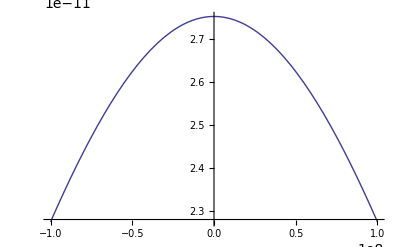

```mathematica
Plot[σmb,{det,-100 *10^6,100*10^6}]
```